CreateDirectory::filex: "C:\\Users\\Petr\\Desktop\\Projects\\sorting\\shown results\\" already exists.

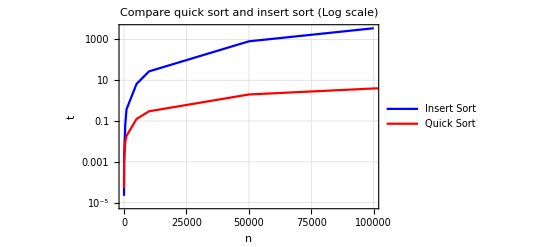

InterpolatingFunction::dmval: Input value {2.04286} lies outside the range of data in the interpolating function. Extrapolation will be used.

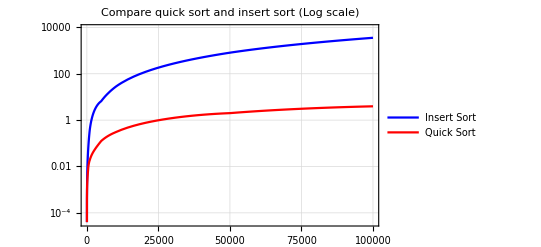

InterpolatingFunction::dmval: Input value {2.04286} lies outside the range of data in the interpolating function. Extrapolation will be used.

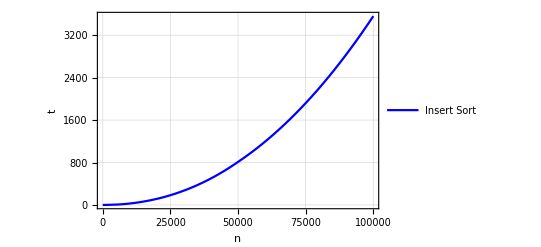

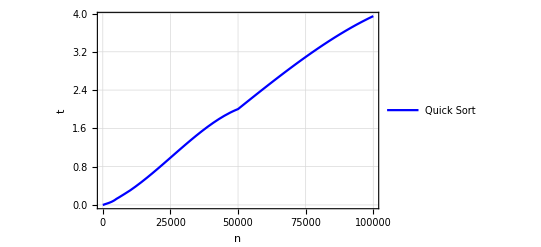

```mathematica
SetDirectory[NotebookDirectory[]];
workingDirectory = CreateDirectory["shown results"];
SetDirectory[workingDirectory];
file= OpenRead["../log.txt"];
filelist= ReadList[file,String];
quickSortResults = filelist[[2;;;;3]];
insertSortResults = filelist[[1;;;;3]];
insertSortResults= Map[({StringSplit[#][[4]],StringSplit[#][[7]]})&,insertSortResults][[;;-4]];
quickSortResults= Map[({StringSplit[#][[4]],StringSplit[#][[7]]})&,quickSortResults];
insertSortResults= Map[({Read[StringToStream[#[[1]]],Number],Read[StringToStream[#[[2]]],Number]})&,insertSortResults];
quickSortResults= Map[({Read[StringToStream[#[[1]]],Number],Read[StringToStream[#[[2]]],Number]})&,quickSortResults];
Plot1 = Show[ListLogPlot[insertSortResults,Joined->True,PlotStyle->Blue,PlotLegends->{"Insert Sort"},PlotLabel->"Compare quick sort and insert sort (Log scale)", AxesLabel->{"n","t"},PlotTheme->"Detailed"],ListLogPlot[quickSortResults,Joined->True,PlotStyle->Red,PlotLegends->{"Quick Sort"}]]
insertFunc = Interpolation[insertSortResults];
quickFunc = Interpolation[quickSortResults];
Plot2 = LogPlot[{insertFunc[x],quickFunc[x]},{x,0,10^5},PlotStyle->{Blue,Red},PlotLegends->{"Insert Sort","Quick Sort"},PlotLabel->"Compare quick sort and insert sort (Log scale)",PlotTheme->"Detailed"]
Plot3 = Plot[insertFunc[x],{x,0,10^5},PlotStyle->Blue,PlotLegends->{"Insert Sort"},AxesLabel->{"n","t"},PlotTheme->"Detailed"]
Plot4 = Plot[quickFunc[x],{x,0,10^5},PlotStyle->Blue,PlotLegends->{"Quick Sort"},AxesLabel->{"n","t"},PlotTheme->"Detailed"]
```

```mathematica
Export["Comp1.gif",Plot1,ImageSize->2048];
Export["Comp2.gif",Plot2,ImageSize->2048];
Export["Insert.gif",Plot3,ImageSize->2048];
Export["Quick.gif",Plot4,ImageSize->2048];
```

```mathematica
grid = Grid[Transpose[{Join[{"Time"},quickSortResults[[All,1]]],Join[{"Insert sort"},insertSortResults[[All,2]],{"-","-","-"}],Join[{"Quick sort"},quickSortResults[[All,2]]]}],Frame->All,Alignment->Left,Background->{None,{Yellow}},ItemStyle->Directive[FontSize->20,Bold]]
```

Time | Insert sort | Quick sort
5 | 0.0000212604 | 0.0000527845
10 | 0.0000777106 | 0.000113633
50 | 0.000882675 | 0.000779672
100 | 0.00279502 | 0.00153295
500 | 0.0656244 | 0.0093535
1000 | 0.371232 | 0.0187206
5000 | 6.53407 | 0.125347
10000 | 27.1463 | 0.299511
50000 | 811.577 | 2.00307
100000 | 3560.33 | 3.94526
500000 | - | 24.1745
1000000 | - | 51.7588
5000000 | - | 323.915

```mathematica
Export["Table.gif",grid,ImageSize->{2048,720}];
Export["Table.xls",grid,ImageSize->{2048,720}];
```